```mathematica
(Normalize[{1,1}].RotationMatrix[θ])
```

{Cos[θ]/(√2)+Sin[θ]/(√2),Cos[θ]/(√2)-Sin[θ]/(√2)}

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
```

(Cos[θ]+Sin[θ]+(Cos[θ]-Sin[θ]) f'[x])/(√2 √(1+f'[x]^2))

```mathematica
y''[t]/((1+y'[t]^2)^(3/2))
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
Element[1,Integers]
```

True

```mathematica
With[{f=Function[x, x x]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))

```mathematica
With[{f=Function[x, x]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

Cos[θ]

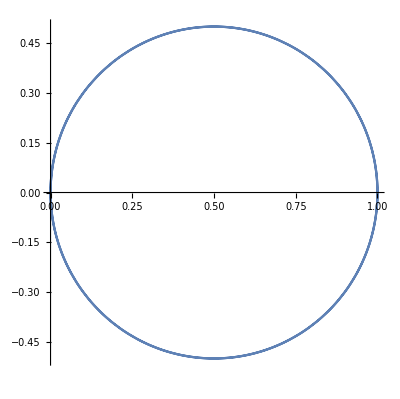

```mathematica
PolarPlot[Cos[θ],{θ,0,2 π}]
```

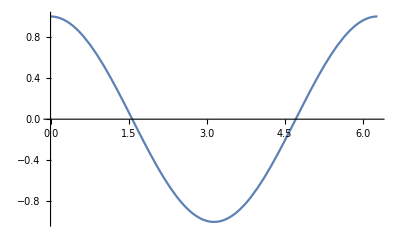

```mathematica
Plot[Cos[θ],{θ,0,2π}]
```

```mathematica
SurfaceData["Cylinder", "ParametricEquations"]
```

Function[a,Function[{u,v},{a Cos[u],a Sin[u],v}]]

```mathematica
Function[a,Function[{u,v},{a Cos[u],a Sin[u],v}]][1][θ,ϕ]
```

{Cos[θ],Sin[θ],ϕ}

```mathematica
ParametricPlot3D[
{Cos[θ],Sin[θ],ϕ}
,{θ,0,2π},{ϕ,0,2π}
]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{Cos[θ],Sin[θ],ϕ}
,{θ,0,2π},{ϕ,0,1}
]
```

-Graphics3D-

```mathematica
∫_a^b √(1+D[u[x],x]^2+(D[F[x,u[x]],x]+D[D[F[x,u[x]],u[x]],x])^2)ⅆx
```

∫_a^b √(1+u'[x]^2+(u'[x] F^(0,1)[x,u[x]]+u'[x] F^(0,2)[x,u[x]]+F^(1,0)[x,u[x]]+F^(1,1)[x,u[x]])^2)ⅆx

```mathematica
√(1+u'[x]^2+(x+u[x] u'[x])^2)
```

√(1+u'[x]^2+(x+u[x] u'[x])^2)

```mathematica
Plot3D[x^2/2+y^2/2,{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
D[√(1+u'[x]^2+(x+u[x] u'[x])^2),u[x]]-D[D[√(1+u'[x]^2+(x+u[x] u'[x])^2),u'[x]],x]==0
```

(u'[x] (x+u[x] u'[x]))/(√(1+u'[x]^2+(x+u[x] u'[x])^2))-(2 u'[x] (x+u[x] u'[x])+2 u''[x]+2 u[x] (1+u'[x]^2+u[x] u''[x]))/(2 √(1+u'[x]^2+(x+u[x] u'[x])^2))+((2 u'[x]+2 u[x] (x+u[x] u'[x])) (2 u'[x] u''[x]+2 (x+u[x] u'[x]) (1+u'[x]^2+u[x] u''[x])))/(4 (1+u'[x]^2+(x+u[x] u'[x])^2)^(3/2))==0

```mathematica
DSolve[%16,{u[x],u[x]},{x}]
```

DSolve[(u'[x] (x+u[x] u'[x]))/(√(1+u'[x]^2+(x+u[x] u'[x])^2))-(2 u'[x] (x+u[x] u'[x])+2 u''[x]+2 u[x] (1+u'[x]^2+u[x] u''[x]))/(2 √(1+u'[x]^2+(x+u[x] u'[x])^2))+((2 u'[x]+2 u[x] (x+u[x] u'[x])) (2 u'[x] u''[x]+2 (x+u[x] u'[x]) (1+u'[x]^2+u[x] u''[x])))/(4 (1+u'[x]^2+(x+u[x] u'[x])^2)^(3/2))==0,{u[x],u[x]},{x}]

```mathematica
With[{L=Identity},
D[L,y[x]]-
D[D[L,y'[x]],x]==0
]
```

True

```mathematica
With[{L=√(1+y'[x]^2)},
D[L,y[x]]-
D[D[L,y'[x]],x]==0
]
```

(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-y''[x]/(√(1+y'[x]^2))==0

```mathematica
DSolve[(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-y''[x]/(√(1+y'[x]^2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
With[{L=2π|y[x]|√(1+y'[x]^2)},
D[L,y[x]]-
D[D[L,y'[x]],x]==0
]
```

(y'[x]^2 y''[x] Alternatives^(0,0,1)[2 π,y[x],√(1+y'[x]^2)])/((1+y'[x]^2)^(3/2))-(y''[x] Alternatives^(0,0,1)[2 π,y[x],√(1+y'[x]^2)])/(√(1+y'[x]^2))+Alternatives^(0,1,0)[2 π,y[x],√(1+y'[x]^2)]-(y'[x] ((y'[x] y''[x] Alternatives^(0,0,2)[2 π,y[x],√(1+y'[x]^2)])/(√(1+y'[x]^2))+y'[x] Alternatives^(0,1,1)[2 π,y[x],√(1+y'[x]^2)]))/(√(1+y'[x]^2))==0

```mathematica
|-1|
```

```mathematica
With[{L=2π Abs[y[x]] √(1+y'[x]^2)},
D[L,y[x]]-
D[D[L,y'[x]],x]==0
]
```

-(2 π Abs'[y[x]] y'[x]^2)/(√(1+y'[x]^2))+2 π Abs'[y[x]] √(1+y'[x]^2)+(2 π Abs[y[x]] y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-(2 π Abs[y[x]] y''[x])/(√(1+y'[x]^2))==0

```mathematica
DSolve[%22,{Abs[y[x]],y[x],y[x]},{x}]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in Abs[y[x]] should literally match the independent variables.

DSolve[-(2 π Abs'[y[x]] y'[x]^2)/(√(1+y'[x]^2))+2 π Abs'[y[x]] √(1+y'[x]^2)+(2 π Abs[y[x]] y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-(2 π Abs[y[x]] y''[x])/(√(1+y'[x]^2))==0,{Abs[y[x]],y[x],y[x]},{x}]

```mathematica
DSolve[-(2 π Abs'[y[x]] y'[x]^2)/(√(1+y'[x]^2))+2 π Abs'[y[x]] √(1+y'[x]^2)+(2 π Abs[y[x]] y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-(2 π Abs[y[x]] y''[x])/(√(1+y'[x]^2))==0,{y[x]},{x}]
```

{{y[x]→InverseFunction[-1/(√(-1+ⅇ^(2 C[1]) Abs[K[1]]^2))K[1]1#1&][x+C[2]]},{y[x]→InverseFunction[1/(√(-1+ⅇ^(2 C[1]) Abs[K[2]]^2))K[2]1#1&][x+C[2]]}}

```mathematica
Activate[InverseFunction[1/(√(-1+ⅇ^(2 C[1]) Abs[K[2]]^2))K[2]1#1&][x+C[2]]]
```

InverseFunction[∫_1^#1 1/(√(-1+ⅇ^(2 C[1]) Abs[K[2]]^2))ⅆK[2]&][x+C[2]]

```mathematica
(∫_1^#1 1/(√(-1+ⅇ^(2 C[1]) Abs[K[2]]^2))ⅆK[2]&)[x+C[2]]
```

$Aborted

```mathematica
Normalize[{x''[t],y''[t]}].Normalize[{-y'[t],x'[t]}]
```

-(y'[t] x''[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2) √(Abs[x''[t]]^2+Abs[y''[t]]^2))+(x'[t] y''[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2) √(Abs[x''[t]]^2+Abs[y''[t]]^2))

```mathematica
FullSimplify[
Normalize[{x''[t],y''[t]}].Normalize[{-y'[t],x'[t]}]
,{t,x'[t],x''[t],y'[t],y''[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))

```mathematica
With[{x=Identity},
(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

y''[t]/(√((1+y'[t]^2) y''[t]^2))

```mathematica
With[{x=Identity,y=Function[x, x x]},
(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

1/(√(1+4 t^2))

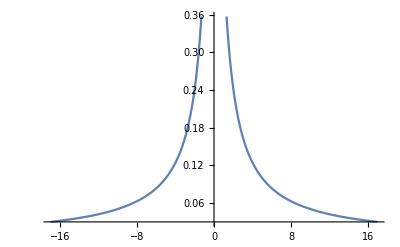

```mathematica
Plot[1/(√(1+4 t^2)),{t,-16.986666666666668,16.986666666666668}]
```

```mathematica
With[{x=Identity,y=Function[x, x]},
(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
With[{x=Identity,y=Function[t, t^2]},
(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

1/(√(1+4 t^2))

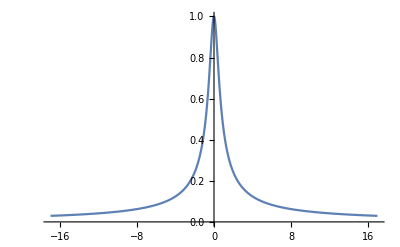

```mathematica
Plot[1/(√(1+4 t^2)),{t,-16.986666666666668,16.986666666666668},PlotRange->{0,1}]
```

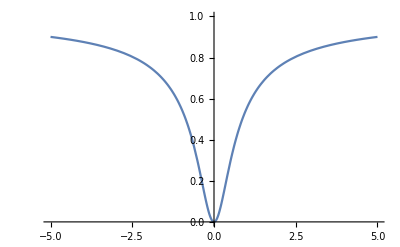

```mathematica
Plot[1-1/(√(1+4 t^2)),{t,-5,5},PlotRange->{0,1}]
```

```mathematica
With[{x=Identity,y=Function[x, x]},
1-(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
With[{x=Identity,y=Function[t,t]},
1-(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
With[{x=Identity,y=Function[t,t^2]},
1-(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

1-1/(√(1+4 t^2))

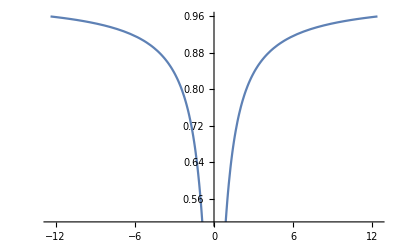

```mathematica
Plot[1-1/(√(1+4 t^2)),{t,-12.376000000000001,12.376000000000001}]
```

```mathematica
With[{x=Identity,y=Log},
1-(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

1+1/(√((1+1/t^2)/t^4) t^2)

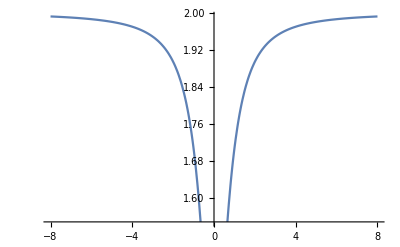

```mathematica
Plot[1+1/(√((1+1/t^2)/t^4) t^2),{t,-8,8}]
```

```mathematica
With[{x=Identity,y=Log},
(-y'[t] x''[t]+x'[t] y''[t])/(√((x'[t]^2+y'[t]^2) (x''[t]^2+y''[t]^2)))
]
```

-1/(√((1+1/t^2)/t^4) t^2)

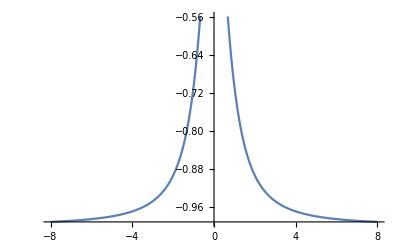

```mathematica
Plot[-1/(√((1+1/t^2)/t^4) t^2),{t,-8,8}]
```

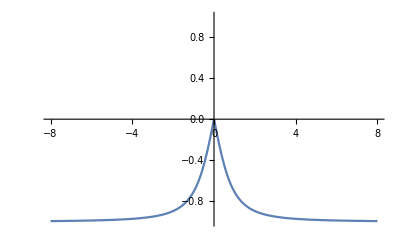

```mathematica
Plot[-1/(√((1+1/t^2)/t^4) t^2),{t,-8,8},PlotRange->{-1,1}]
```

```mathematica
f[x]==f[x-α]+f[α]
```

f[x]==f[x-α]+f[α]

```mathematica
f[x]==f[x-α]+α
```

f[x]==α+f[x-α]

```mathematica
With[{f=Function[x, x x]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))

```mathematica
Manipulate[Plot[(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2)),{x,-1.2218141834561118,2.7918099101556484}],{θ,0,2π}]
```

```mathematica
With[{f=Function[x,x^3]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 Abs[x]^4))

```mathematica
Manipulate[Plot[(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 Abs[x]^4)),{x,-1.9721401103196348,1.9721401103196348}],{θ,-2.0943951023931953,2.0943951023931953}]
```

```mathematica
(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 x^4))
```

(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 x^4))

```mathematica
Manipulate[Plot[(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 x^4)),{x,0.2861501135343747,2.279345347825778}],{θ,0,2π}]
```

```mathematica
Plot3D[(Cos[θ]+3 x^2 Cos[θ]+Sin[θ]-3 x^2 Sin[θ])/(√(2+18 x^4)),{x,-3,3},{θ,0,2π}]
```

-Graphics3D-

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::outdcache: Using potentially outdated cached values.

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][θ,ϕ]
```

{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}

```mathematica
Norm[D[{Cos[θ[t]] Sin[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[ϕ[t]]},t]]
```

√(Abs[Sin[ϕ[t]] ϕ'[t]]^2+Abs[-Sin[θ[t]] Sin[ϕ[t]] θ'[t]+Cos[θ[t]] Cos[ϕ[t]] ϕ'[t]]^2+Abs[Cos[θ[t]] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] Sin[θ[t]] ϕ'[t]]^2)

```mathematica
FullSimplify[
Norm[D[{Cos[θ[t]] Sin[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[ϕ[t]]},t]]
,{t,θ[t],ϕ[t]}∈Reals]
```

√(Abs[Sin[ϕ[t]] ϕ'[t]]^2+Abs[Sin[θ[t]] Sin[ϕ[t]] θ'[t]-Cos[θ[t]] Cos[ϕ[t]] ϕ'[t]]^2+Abs[Cos[θ[t]] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] Sin[θ[t]] ϕ'[t]]^2)

```mathematica
FullSimplify[
Norm[D[{Cos[θ[t]] Sin[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[ϕ[t]]},t]]
,{t,θ[t],ϕ[t],θ'[t],ϕ'[t]}∈Reals]
```

√(Sin[ϕ[t]]^2 θ'[t]^2+ϕ'[t]^2)

```mathematica
√(Sin[ϕ]^2 θ'[ϕ]^2+1)
```

√(1+Sin[ϕ]^2 θ'[ϕ]^2)

```mathematica
With[{L=√(1+Sin[x]^2 y'[x]^2)},
D[L,y[x]]-
D[D[L,y'[x]],x]==0
]
```

-(2 Cos[x] Sin[x] y'[x])/(√(1+Sin[x]^2 y'[x]^2))-(Sin[x]^2 y''[x])/(√(1+Sin[x]^2 y'[x]^2))+(Sin[x]^2 y'[x] (2 Cos[x] Sin[x] y'[x]^2+2 Sin[x]^2 y'[x] y''[x]))/(2 (1+Sin[x]^2 y'[x]^2)^(3/2))==0

```mathematica
DSolve[%63,{y[x],y[x]},{x}]
```

{{y[x]→C[2]-(ArcTan[(√2 Cos[x])/(√(-2+C[1]-C[1] Cos[2 x]))] Sin[x] √(-1+C[1] Sin[x]^2))/(√(Sin[x]^2 (-1+C[1] Sin[x]^2)))},{y[x]→C[2]+(ArcTan[(√2 Cos[x])/(√(-2+C[1]-C[1] Cos[2 x]))] Sin[x] √(-1+C[1] Sin[x]^2))/(√(Sin[x]^2 (-1+C[1] Sin[x]^2)))}}

```mathematica
(ArcTan[(√2 Cos[x])/(√(-2+C[1]-C[1] Cos[2 x]))] Sin[x] √(-1+C[1] Sin[x]^2))/(√(Sin[x]^2 (-1+C[1] Sin[x]^2)))/.C[1]->1
```

(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2)))

```mathematica
Plot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-2,2}]
```

-Graphics-

```mathematica
(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2)))/.x->10
```

ⅈ ArcTanh[Cos[10] √(2/(1+Cos[20]))]

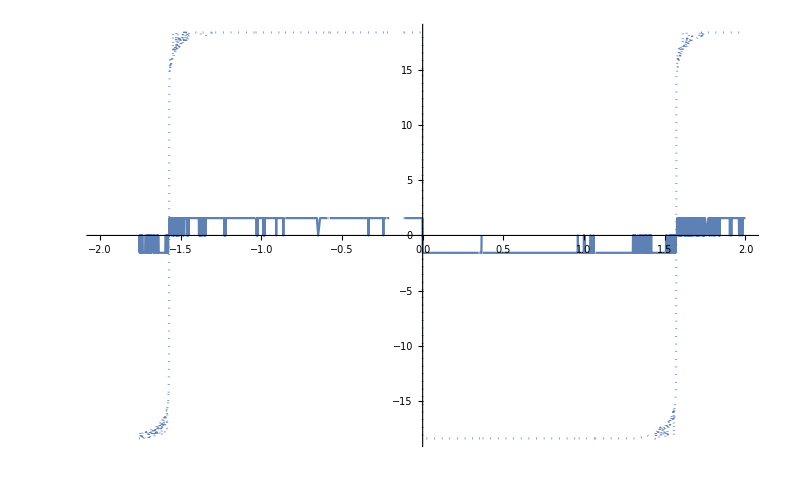

```mathematica
ReImPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-2,2}]
```

```mathematica
ComplexPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-2,2}]
```

ComplexPlot::plld: Corners for x in {x,-2,2} must have distinct machine-precision real and imaginary parts.

ComplexPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-2,2}]

```mathematica
ComplexPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-1-I,1+I}]
```

-Graphics-

```mathematica
With[{f=Function[x, x x]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

(Cos[θ]+2 x Cos[θ]+Sin[θ]-2 x Sin[θ])/(√(2+8 x^2))

```mathematica
ComplexPlot[(ArcTan[(√2 Cos[x])/(√(-1-Cos[2 x]))] Sin[x] √(-1+Sin[x]^2))/(√(Sin[x]^2 (-1+Sin[x]^2))),{x,-1/2-I/2,1/2+I/2}]
```

-Graphics-

```mathematica
With[{f=Function[x, Sin[x]]},
FullSimplify[
Normalize[{1,f'[x]}].(Normalize[{1,1}].RotationMatrix[θ])
,{θ,f'[x]}∈Reals∧0≤θ≤2π]
]
```

(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x]))

```mathematica
Manipulate[Plot[(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x])),{x,-3.11150666626932,16.00373866175642}],{θ,0,2π}]
```

```mathematica
Manipulate[Plot[(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x])),{θ,0,2π}],{x,-2π,2π}]
```

```mathematica
Plot3D[(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x])),{x,-10,-10},{θ,0,2 π}]
```

Plot3D::plld: Endpoints for x in {x,-10,-10} must have distinct machine-precision numerical values.

Plot3D[(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x])),{x,-10,-10},{θ,0,2 π}]

```mathematica
Plot3D[(Cos[θ]+Cos[x] (Cos[θ]-Sin[θ])+Sin[θ])/(√(3+Cos[2 x])),{x,-10,10},{θ,0,2 π}]
```

-Graphics3D-

```mathematica
Dt[F[x,y[x],y'[x]]]
```

Dt[x] y''[x] F^(0,0,1)[x,y[x],y'[x]]+Dt[x] y'[x] F^(0,1,0)[x,y[x],y'[x]]+Dt[x] F^(1,0,0)[x,y[x],y'[x]]

```mathematica
Dt[x] y''[x] Derivative[0,0,1][F][x,y[x],y'[x]]+Dt[x] y'[x] Derivative[0,1,0][F][x,y[x],y'[x]]+Dt[x] Derivative[1,0,0][F][x,y[x],y'[x]]/.Dt[x]->1
```

y''[x] F^(0,0,1)[x,y[x],y'[x]]+y'[x] F^(0,1,0)[x,y[x],y'[x]]+F^(1,0,0)[x,y[x],y'[x]]

```mathematica
Dt[Composition[a,b,c,d,e][x]]
```

Dt[x] a'[b[c[d[e[x]]]]] b'[c[d[e[x]]]] c'[d[e[x]]] d'[e[x]] e'[x]

```mathematica
D[Composition[a,b,c,d,e][x],x]
```

a'[b[c[d[e[x]]]]] b'[c[d[e[x]]]] c'[d[e[x]]] d'[e[x]] e'[x]

```mathematica
Dt[x==r Cos[θ]Sin[ϕ]]
```

Dt[x]==r Cos[θ] Cos[ϕ] Dt[ϕ]+Cos[θ] Dt[r] Sin[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ]

```mathematica
Dt[x]==r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ]
```

Dt[x]==r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ]

```mathematica
√(Dt[x]^2+Dt[y]^2+Dt[z]^2)
```

√(Dt[x]^2+Dt[y]^2+Dt[z]^2)

```mathematica
Dt[y==r Sin[θ]Sin[ϕ]]
```

Dt[y]==r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ]+Dt[r] Sin[θ] Sin[ϕ]

```mathematica
Dt[y==r Sin[θ]Sin[ϕ]]/.Dt[r]->0
```

Dt[y]==r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ]

```mathematica
Dt[z==r Cos[ϕ]]
```

Dt[z]==Cos[ϕ] Dt[r]-r Dt[ϕ] Sin[ϕ]

```mathematica
√(Dt[x]^2+Dt[y]^2+Dt[z]^2)/.{Dt[x]->r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ],Dt[y]->r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ],Dt[z]->r Dt[ϕ] Sin[ϕ]}
```

√(r^2 Dt[ϕ]^2 Sin[ϕ]^2+(r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ])^2+(r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ])^2)

```mathematica
FullSimplify[
√(r^2 Dt[ϕ]^2 Sin[ϕ]^2+(r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ])^2+(r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ])^2)
,{r,θ,ϕ,Dt[θ],Dt[ϕ]}∈Reals]
```

Abs[r] √(Dt[ϕ]^2+Dt[θ]^2 Sin[ϕ]^2)

```mathematica
FullSimplify[
√(r^2 Dt[ϕ]^2 Sin[ϕ]^2+(r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ])^2+(r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ])^2)
,{r,θ,ϕ,Dt[θ],Dt[ϕ]}∈Reals∧0≤θ≤2π∧0≤ϕ≤2π]
```

Abs[r] √(Dt[ϕ]^2+Dt[θ]^2 Sin[ϕ]^2)

```mathematica
r √((Dt[ϕ]/Dt[ϕ])^2+(Dt[θ]/Dt[ϕ])^2 Sin[ϕ]^2)
```

r √(1+(Dt[θ]^2 Sin[ϕ]^2)/Dt[ϕ]^2)

```mathematica
D[r √(1+Sin[ϕ]^2 θ'[ϕ]^2),θ[ϕ]]-D[D[r √(1+Sin[ϕ]^2 θ'[ϕ]^2),θ'[ϕ]],ϕ]==0
```

-(2 r Cos[ϕ] Sin[ϕ] θ'[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))-(r Sin[ϕ]^2 θ''[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))+(r Sin[ϕ]^2 θ'[ϕ] (2 Cos[ϕ] Sin[ϕ] θ'[ϕ]^2+2 Sin[ϕ]^2 θ'[ϕ] θ''[ϕ]))/(2 (1+Sin[ϕ]^2 θ'[ϕ]^2)^(3/2))==0

```mathematica
DSolve[%93,{θ[ϕ],θ[ϕ]},{r,ϕ}]
```

DSolve::alliv: The function θ[ϕ] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[-(2 r Cos[ϕ] Sin[ϕ] θ'[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))-(r Sin[ϕ]^2 θ''[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))+(r Sin[ϕ]^2 θ'[ϕ] (2 Cos[ϕ] Sin[ϕ] θ'[ϕ]^2+2 Sin[ϕ]^2 θ'[ϕ] θ''[ϕ]))/(2 (1+Sin[ϕ]^2 θ'[ϕ]^2)^(3/2))==0,{θ[ϕ],θ[ϕ]},{r,ϕ}]

```mathematica
r √((Dt[ϕ]/Dt[ϕ])^2+(Dt[θ[ϕ]]/Dt[ϕ])^2 Sin[ϕ]^2)
```

r √(1+Sin[ϕ]^2 θ'[ϕ]^2)

```mathematica
DSolve[%93,{θ[ϕ]},{r,ϕ}]
```

DSolve::alliv: The function θ[ϕ] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[-(2 r Cos[ϕ] Sin[ϕ] θ'[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))-(r Sin[ϕ]^2 θ''[ϕ])/(√(1+Sin[ϕ]^2 θ'[ϕ]^2))+(r Sin[ϕ]^2 θ'[ϕ] (2 Cos[ϕ] Sin[ϕ] θ'[ϕ]^2+2 Sin[ϕ]^2 θ'[ϕ] θ''[ϕ]))/(2 (1+Sin[ϕ]^2 θ'[ϕ]^2)^(3/2))==0,{θ[ϕ]},{r,ϕ}]

```mathematica
DSolve[%93,{θ[ϕ]},{ϕ}]
```

{{θ[ϕ]→C[2]-(ArcTan[(√2 Cos[ϕ])/(√(-2+C[1]-C[1] Cos[2 ϕ]))] Sin[ϕ] √(-1+C[1] Sin[ϕ]^2))/(√(Sin[ϕ]^2 (-1+C[1] Sin[ϕ]^2)))},{θ[ϕ]→C[2]+(ArcTan[(√2 Cos[ϕ])/(√(-2+C[1]-C[1] Cos[2 ϕ]))] Sin[ϕ] √(-1+C[1] Sin[ϕ]^2))/(√(Sin[ϕ]^2 (-1+C[1] Sin[ϕ]^2)))}}

```mathematica
r √((Dt[ϕ]/Dt[ϕ])^2+(Dt[θ[ϕ]]/Dt[ϕ])^2 Sin[ϕ]^2)
```

r √(1+Sin[ϕ]^2 θ'[ϕ]^2)

```mathematica
FullSimplify[
√(r^2 Dt[ϕ]^2 Sin[ϕ]^2+(r Cos[ϕ] Dt[ϕ] Sin[θ]+r Cos[θ] Dt[θ] Sin[ϕ])^2+(r Cos[θ] Cos[ϕ] Dt[ϕ]-r Dt[θ] Sin[θ] Sin[ϕ])^2)
,{r,θ,ϕ,Dt[θ],Dt[ϕ]}∈Reals∧0≤θ≤2π∧0≤ϕ≤2π]
```

Abs[r] √(Dt[ϕ]^2+Dt[θ]^2 Sin[ϕ]^2)

```mathematica
Dt[f[x]g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
x+y+z==0
```

x+y+z==0

```mathematica
ContourPlot3D[x+y+z==0,{x,y,z}∈Sphere[]]
```

ContourPlot3D::idomdim: {x,y,z}∈Sphere[] does not have a valid dimension as a plotting domain.

ContourPlot3D[x+y+z==0,{x,y,z}∈Sphere[]]

```mathematica
ContourPlot3D[x+y+z==0,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][r][θ,ϕ]
```

{r Cos[θ] Sin[ϕ],r Sin[θ] Sin[ϕ],r Cos[ϕ]}

```mathematica
{ Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
```

{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}

```mathematica
A x+B y+ C z==0
```

A x+B y+C z==0

```mathematica
A x+B y+ C z==0/.{x->Cos[θ] Sin[ϕ],y->Sin[θ] Sin[ϕ],z->Cos[ϕ]}
```

C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==0

```mathematica
DivideSides[C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==0,Sin[ϕ]]
```

Piecewise[{{Csc[ϕ] (C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ])==0, Sin[ϕ]≠0}, {C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==0, True}}]

```mathematica
SubtractSides[C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==0,Cos[ϕ]]
```

-Cos[ϕ]+C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==-Cos[ϕ]

```mathematica
DivideSides[SubtractSides[C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==0,Cos[ϕ]],Sin[ϕ]]
```

Piecewise[{{Csc[ϕ] (-Cos[ϕ]+C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ])==-Cot[ϕ], Sin[ϕ]≠0}, {-Cos[ϕ]+C Cos[ϕ]+A Cos[θ] Sin[ϕ]+B Sin[θ] Sin[ϕ]==-Cos[ϕ], True}}]

```mathematica
Dt[a b c d]
```

b c d Dt[a]+a c d Dt[b]+a b d Dt[c]+a b c Dt[d]

```mathematica
plist=Table[{(4 i-26)/6,-(-1)^i},{i,1,12}];r[{xi_,yi_}]:=Sqrt[(x-xi)^2+(y-yi)^2];
DensityPlot[2Sqrt[((Plus@@Map[#[[2]](x-#[[1]])/r[#]^2&,plist])^2+(Plus@@Map[-#[[2]](y-#[[2]])/r[#]^2&,plist])^2)]+Cos[18.8Plus@@Map[#[[2]]/r[#]&,plist]]+1,{x,-6,6},{y,-3,3},Mesh->False,Frame->False,PlotRange->{0,10},PlotPoints->{275,138},AspectRatio->1/2]
```

-Graphics-

```mathematica
MemoryInUse[]
```

373140952

```mathematica
SurfaceData["Cylinder","ParametricEquations"]
```

Function[a,Function[{u,v},{a Cos[u],a Sin[u],v}]]

```mathematica
Function[a,Function[{u,v},{a Cos[u],a Sin[u],v}]][1][θ,ϕ]
```

{Cos[θ],Sin[θ],ϕ}

```mathematica
√(Dt[x]^2+Dt[y]^2+Dt[z]^2)
```

√(Dt[x]^2+Dt[y]^2+Dt[z]^2)

```mathematica
{Dt[x==Cos[θ]],Dt[y==Sin[θ]],Dt[z=ϕ]}
```

{Dt[x]==-Dt[θ] Sin[θ],Dt[y]==Cos[θ] Dt[θ],Dt[ϕ]}

```mathematica
z
```

ϕ

```mathematica
Clear[z]
```

```mathematica
ClearAll[z]
```

```mathematica
√(Dt[x]^2+Dt[y]^2+Dt[z]^2)/.{Dt[x]->-Dt[θ] Sin[θ],Dt[y]-> Cos[θ] Dt[θ],Dt[z]->Dt[ϕ]}
```

√(Cos[θ]^2 Dt[θ]^2+Dt[ϕ]^2+Dt[θ]^2 Sin[θ]^2)

```mathematica
FullSimplify[
√(Cos[θ]^2 Dt[θ]^2+Dt[ϕ]^2+Dt[θ]^2 Sin[θ]^2)
,{θ,ϕ}∈Reals]
```

√(Dt[θ]^2+Dt[ϕ]^2)

```mathematica
√((Dt[θ]/Dt[ϕ])^2+(Dt[ϕ]/Dt[ϕ])^2)
```

√(1+Dt[θ]^2/Dt[ϕ]^2)

```mathematica
√(1+Dt[θ[ϕ]]^2/Dt[ϕ]^2)
```

√(1+θ'[ϕ]^2)

```mathematica
D[√(1+θ'[ϕ]^2),θ[ϕ]]-D[D[√(1+θ'[ϕ]^2),θ'[ϕ]],ϕ]==0
```

(θ'[ϕ]^2 θ''[ϕ])/((1+θ'[ϕ]^2)^(3/2))-θ''[ϕ]/(√(1+θ'[ϕ]^2))==0

```mathematica
DSolve[(θ'[ϕ]^2 θ''[ϕ])/((1+θ'[ϕ]^2)^(3/2))-θ''[ϕ]/(√(1+θ'[ϕ]^2))==0,{θ[ϕ],θ[ϕ]},{ϕ}]
```

{{θ[ϕ]→C[1]+ϕ C[2]}}

```mathematica
(1-a)p+a q/.{p->{0,0,0},q->{Cos[θ],Sin[θ],ϕ}}
```

{a Cos[θ],a Sin[θ],a ϕ}

```mathematica
Manipulate[
ParametricPlot3D[
{a Cos[θ],a Sin[θ],a ϕ}
,{θ,0,2π},{ϕ,0,2π}
],{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot3D[
{a Cos[θ],a Sin[θ],a ϕ}
,{θ,0,2π},{ϕ,0,2π}
,PlotRange->{{-1,1},{-1,1},{-1,1}}]
,{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{θ,ϕ,0},q->{Cos[θ],Sin[θ],ϕ}}
```

{(1-a) θ+a Cos[θ],(1-a) ϕ+a Sin[θ],a ϕ}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) θ+a Cos[θ],(1-a) ϕ+a Sin[θ],a ϕ}
,{θ,0,2π},{ϕ,0,2π}
,PlotRange->{{-1,1},{-1,1},{-1,1}}]
,{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) θ+a Cos[θ],(1-a) ϕ+a Sin[θ],a ϕ}
,{θ,0,2π},{ϕ,0,2π}
,PlotRange->{{-2,2},{-2,2},{-2,2}}]
,{a,0,1}]
```

```mathematica
SurfaceData["Torus","ParametricEquations"]
```

Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]]

```mathematica
Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]][1/2,1][θ,ϕ]
```

```mathematica
(1-a)p+a q/.{p->{Cos[θ],Sin[θ],ϕ},q->{Cos[θ] (1+Cos[ϕ]/2),(1+Cos[ϕ]/2) Sin[θ],Sin[ϕ]/2}}
```

{(1-a) Cos[θ]+a Cos[θ] (1+Cos[ϕ]/2),(1-a) Sin[θ]+a (1+Cos[ϕ]/2) Sin[θ],(1-a) ϕ+1/2 a Sin[ϕ]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[θ]+a Cos[θ] (1+Cos[ϕ]/2),(1-a) Sin[θ]+a (1+Cos[ϕ]/2) Sin[θ],(1-a) ϕ+1/2 a Sin[ϕ]}
,{θ,0,2π},{ϕ,0,2π}
,PlotRange->{{-2,2},{-2,2},{-2,2}}]
,{a,0,1}]
```